# SpinDynamica Bruker Data Loader Tutorial 01: Importing and Working with 1D Spectra

## Loading TopSpin 1D datasets (1r/1i, procs/acqus), intensity scaling, NMR plotting conventions, phasing and combining spectra, and converting to time-domain Signal objects.

## 0. Setup and Loading SpinDynamica

Evaluate both setup cells in order. Cell 1 locates the SpinDynamica repository root upward from NotebookDirectory[] using System` symbols only and loads SpinDynamica`; Cell 2 verifies that Signals`Bruker` loaded cleanly and sets sampleDir to the bundled TopSpin 1D dataset.

```mathematica
nbRepoRoot=Quiet[Check[NotebookDirectory[],Directory[]]];
While[StringQ[nbRepoRoot]&&nbRepoRoot=!=""&&!FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],With[{parent=ParentDirectory[nbRepoRoot]},If[parent===nbRepoRoot,nbRepoRoot=Directory[];Break[],nbRepoRoot=parent]]];
If[FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`",FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`"]];
```

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator, Duration, Exp, Expand, Plus, Power, Simplify, SolidAngle, Times, WignerD}

```mathematica
sampleDir=FileNameJoin[{nbRepoRoot,"sample_data"}];
{MemberQ[$Packages,"Signals`Bruker`"],Context[ImportBrukerSpectrum],DirectoryQ[sampleDir]}
```

{True,Signals`Bruker`,True}

## 1. Your First Bruker Import and Spectrum Plot

ImportBrukerSpectrum reads processed TopSpin 1D datasets automatically from an experiment root directory, a pdata directory, a processed directory (such as pdata/1), or directly from a 1r binary file. You can also select a specific processing number with ProcessingNumber -> n.

```mathematica
spec=ImportBrukerSpectrum[sampleDir]
```

BrukerSpectrum[1H, 131072 pts, SF=299.83 MHz, 8.338..-8.338 ppm, complex]

All four path styles yield identical spectral data:

```mathematica
specPdata=ImportBrukerSpectrum[FileNameJoin[{sampleDir,"pdata"}],ProcessingNumber->1];
spec1r=ImportBrukerSpectrum[FileNameJoin[{sampleDir,"pdata","1","1r"}]];
{"Max |expDir - pdata|"->Max[Abs[spec["Real"]-specPdata["Real"]]],"Max |expDir - 1r|"->Max[Abs[spec["Real"]-spec1r["Real"]]]}
```

{Max |expDir - pdata|→0.,Max |expDir - 1r|→0.}

Let us immediately inspect the full 1H spectrum and a zoom around the dominant peak near -1.99 ppm using PlotBrukerSpectrum (passing MaxPlotPoints -> 4000 so the 131,072-point full trace plots cleanly and interactively).

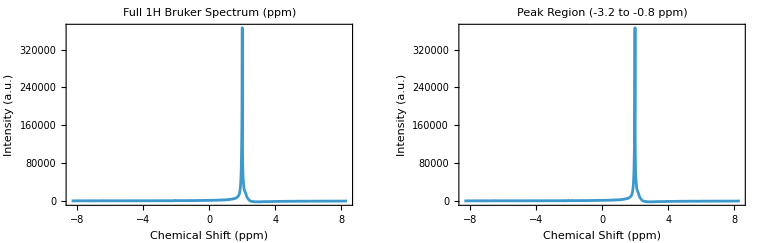

```mathematica
GraphicsRow[{PlotBrukerSpectrum[spec,MaxPlotPoints->4000,PlotLabel->"Full 1H Bruker Spectrum (ppm)"],PlotBrukerSpectrum[spec,MaxPlotPoints->4000,PlotRange->{{-3.2,-0.8},All},PlotLabel->"Peak Region (-3.2 to -0.8 ppm)"]},ImageSize->760,Spacings->25]
```

## 2. Inspecting BrukerSpectrum Properties and JCAMP-DX Parameters

BrukerSpectrum behaves like an Association for scalar properties, calibrated axes, spectral arrays, and parsed TopSpin parameter files. Querying "Properties" lists every supported key, and "Metadata" returns all metadata without dumping large 1D arrays.

```mathematica
{"PropertyCount"->Length[spec["Properties"]],"SampleProperties"->Take[spec["Properties"],14]}
```

{PropertyCount→41,SampleProperties→{AcquisitionParameters,AngularFrequency,AppliedScaleFactor,BrukerScaleFactor,ByteOrder,BYTORDP,ChemicalShift,Complex,DataType,DTYPP,ExperimentDirectory,Frequency,HasImaginary,Hz}}

```mathematica
Dataset[KeyTake[spec["Metadata"],{"Nucleus","ReferenceFrequencyMHz","SpectralWidthHz","SpectralWidthPPM","NumPoints","NCProc","BrukerScaleFactor","ByteOrder","DataType","HasImaginary"}]]
```

Full JCAMP-DX dictionaries from procs and acqus are stored under "ProcessingParameters" and "AcquisitionParameters", and you can also parse any parameter file standalone using ReadBrukerParameters. Passing ReadAcquisitionParameters -> False skips reading acqus when only processed metadata is needed.

```mathematica
procs=ReadBrukerParameters[FileNameJoin[{sampleDir,"pdata","1","procs"}]];
acqus=spec["AcquisitionParameters"];
specNoAcq=ImportBrukerSpectrum[sampleDir,ReadAcquisitionParameters->False];
{"procs (SI, SF, SW_p, OFFSET, NC_proc, LB, PHC0)"->KeyTake[procs,{"SI","SF","SW_p","OFFSET","NC_proc","LB","PHC0"}],"acqus (PULPROG, TD, NS, RG)"->KeyTake[acqus,{"PULPROG","TD","NS","RG"}],"ReadAcquisitionParameters -> False"->specNoAcq["AcquisitionParameters"]}
```

{procs (SI, SF, SW_p, OFFSET, NC_proc, LB, PHC0)→<|SI→131072,SF→299.833,SW_p→5000,OFFSET→8.33798,NC_proc→-10,LB→1,PHC0→113.2|>,acqus (PULPROG, TD, NS, RG)→<|PULPROG→gp_echozg,TD→65536,NS→1,RG→64|>,ReadAcquisitionParameters -> False→<||>}

## 3. Intensity Scaling, Imaginary Data, and Return Formats

TopSpin stores 1r/1i integers scaled by an exponent NC_proc (here NC_proc = -10, corresponding to a multiplier of 2^-10). IntensityScaling controls how loaded intensities are scaled:
  - "Bruker" (default): multiplies stored integers by 2^NC_proc.
  - "Raw": keeps raw stored integers unscaled.
  - "Normalized": applies 2^NC_proc and scales peak magnitude to 1.
  - Positive number (e.g. 10^-6): multiplies 2^NC_proc by your custom factor.
Additional options: IncludeRawData -> False omits RawReal/RawImaginary arrays to save memory; ReadImaginary -> False skips 1i; ReturnFormat returns "BrukerSpectrum" (default), "Association", or coordinate pairs "Pairs" (supporting AxisOrder -> Automatic | "Ascending" | "Descending").

```mathematica
specRaw=ImportBrukerSpectrum[sampleDir,IntensityScaling->"Raw"];
specNorm=ImportBrukerSpectrum[sampleDir,IntensityScaling->"Normalized"];
specCustom=ImportBrukerSpectrum[sampleDir,IntensityScaling->1.*^-6];
specRealOnly=ImportBrukerSpectrum[sampleDir,ReadImaginary->False,IncludeRawData->False];
pairsHzAsc=ImportBrukerSpectrum[sampleDir,ReturnFormat->"Pairs",AxisUnits->"Hz",AxisOrder->"Ascending"];
TableForm[{{"Bruker (default, 2^NC_proc)",Max[spec["Real"]],spec["AppliedScaleFactor"],spec["HasImaginary"]},{"Raw",Max[specRaw["Real"]],specRaw["AppliedScaleFactor"],specRaw["HasImaginary"]},{"Normalized",Max[Abs[specNorm["Complex"]]],specNorm["AppliedScaleFactor"],specNorm["HasImaginary"]},{"Custom (10^-6)",Max[specCustom["Real"]],specCustom["AppliedScaleFactor"],specCustom["HasImaginary"]},{"ReadImaginary -> False",Max[specRealOnly["Real"]],specRealOnly["RawReal"],specRealOnly["HasImaginary"]}},TableHeadings->{None,{"Mode","Max Amplitude","ScaleFactor / RawReal","HasImaginary"}}]
```

Mode | Max Amplitude | ScaleFactor / RawReal | HasImaginary
Bruker (default, 2^NC_proc) | 378796. | 0.000976563 | True
Raw | 387887124 | 1. | True
Normalized | 1. | 2.49874×10^-9 | True
Custom (10^-6) | 0.378796 | 9.76563×10^-10 | True
ReadImaginary -> False | 378796. | None | False

```mathematica
{"ReturnFormat -> Pairs Length"->Length[pairsHzAsc],"First & Last Hz (Ascending)"->{pairsHzAsc[[1,1]],pairsHzAsc[[-1,1]]}}
```

{ReturnFormat -> Pairs Length→131072,First & Last Hz (Ascending)→{-2500.,2500.}}

## 4. Plotting Conventions and Spectral Components

PlotBrukerSpectrum (also aliased via ListPlot[spec, ...]) adapts to AxisUnits -> "ppm" | "Hz" | "rad/s", ReverseAxis -> Automatic | True | False (ReverseAxis -> Automatic reverses chemical shift ppm left-to-right per NMR convention while keeping Hz and rad/s ascending), and Component -> "Real" | "Imaginary" | "Both" | "Complex" | "Magnitude".

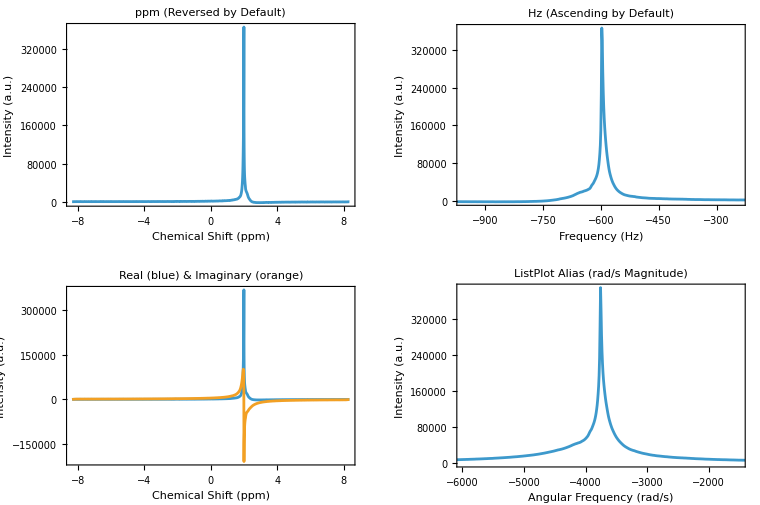

```mathematica
GraphicsGrid[{{PlotBrukerSpectrum[spec,AxisUnits->"ppm",Component->"Real",MaxPlotPoints->4000,PlotRange->{{-3.2,-0.8},All},PlotLabel->"ppm (Reversed by Default)"],PlotBrukerSpectrum[spec,AxisUnits->"Hz",Component->"Real",MaxPlotPoints->4000,PlotRange->{{-960,-240},All},PlotLabel->"Hz (Ascending by Default)"]},{PlotBrukerSpectrum[spec,AxisUnits->"ppm",Component->"Both",MaxPlotPoints->4000,PlotRange->{{-3.2,-0.8},All},PlotLegends->None,PlotLabel->"Real (blue) & Imaginary (orange)"],ListPlot[spec,AxisUnits->"rad/s",Component->"Magnitude",MaxPlotPoints->4000,PlotRange->{{-6000,-1500},All},PlotLabel->"ListPlot Alias (rad/s Magnitude)"]}},ImageSize->760,Spacings->{20,15}]
```

## 5. Extracting Pairs, Peak Finding, Phasing, and Combining Spectra

BrukerSpectrum supports SpinDynamica data UpValues directly: Length[spec], Expand[spec, AxisUnits -> ..., Component -> ..., AxisOrder -> ...] (equivalently spec["Pairs", units, comp, order]), Re[spec], Im[spec], Abs[spec], numeric/complex scalar multiplication (such as Exp[I * phi] * spec for zero-order phase adjustment), and linear combination via CombineData.

```mathematica
peakIdx=First[Ordering[spec["Real"],-1]];
specPhased=Exp[I*(35.*Degree)]*spec;
specAvg=CombineData[{spec,specPhased},{0.5,0.5}];
{"Length[spec]"->Length[spec],"Peak Position (ppm, Hz)"->{spec["PPM"][[peakIdx]],spec["Hz"][[peakIdx]]},"Max |Expand[spec] - Re[spec]|"->Max[Abs[Expand[spec][[All,2]]-Re[spec][[All,2]]]],"Peak Amp (Original, +35 deg, Combined)"->{Max[spec["Real"]],Max[specPhased["Real"]],Max[specAvg["Real"]]}}
```

{Length[spec]→131072,Peak Position (ppm, Hz)→{-1.99335,-597.672},Max |Expand[spec] - Re[spec]|→0.,Peak Amp (Original, +35 deg, Combined)→{378796.,378439.,372730.}}

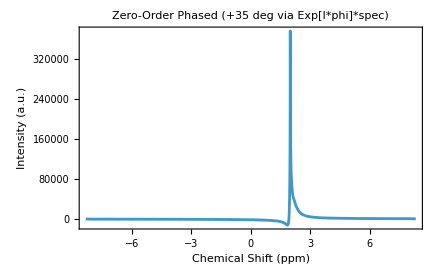

```mathematica
PlotBrukerSpectrum[specPhased,MaxPlotPoints->4000,PlotRange->{{-3.2,-0.8},All},PlotLabel->"Zero-Order Phased (+35 deg via Exp[I*phi]*spec)",ImageSize->440]
```

## 6. Converting to a SpinDynamica Signal (ToSignal) and FT Processing

ToSignal[spec] transforms an imported 1D BrukerSpectrum back into a SpinDynamica time-domain Signal object via inverse FFT on SpinDynamica's frequency convention. You can verify the exact round-trip with FT[sigExp, ZeroFill -> 1, FirstPointMultiplicationFactor -> 1] (error ~ 3e-16), and apply SpinDynamica processing such as ApplyLineBroadening. Because sample_data was acquired with a spin-echo (gp_echozg) sequence over 26.2 s, half of the inverse-FFT echo signal sits near t = 0 and the anti-causal echo wing wraps to t -> 26.2 s; therefore a gentle LineBroadening -> 0.05 rad/s cleanly reduces and broadens the peak without suppressing the wrapped echo wing.

```mathematica
sigExp=ToSignal[spec];
ftRoundTrip=FT[sigExp,ZeroFill->1,FirstPointMultiplicationFactor->1];
roundTripErr=Max[Abs[Reverse[ftRoundTrip[[All,2]]]-spec["Complex"]]]/Max[Abs[spec["Complex"]]];
sigBroad=ApplyLineBroadening[sigExp,LineBroadening->0.05];
ftBroad=FT[sigBroad,ZeroFill->1,FirstPointMultiplicationFactor->1];
{"Signal Sampling {tmin, tmax, dt}"->First[sigExp],"FT Round-Trip Relative Error"->roundTripErr,"Peak Ratio after 0.05 rad/s Broadening"->Max[Re[ftBroad[[All,2]]]]/Max[spec["Real"]]}
```

{Signal Sampling {tmin, tmax, dt}→{0.,26.2142,0.0002},FT Round-Trip Relative Error→3.33033×10^-16,Peak Ratio after 0.05 rad/s Broadening→0.522072}

```mathematica
tGrid=Range[First[sigExp][[1]],First[sigExp][[2]],First[sigExp][[3]]];
GraphicsRow[{ListLinePlot[Transpose[{tGrid[[1;;800]],Abs[sigExp[[2,1;;800]]]}],Frame->True,PlotRange->All,FrameLabel->{"Time (s)","|FID|"},PlotLegends->Placed[{"|FID| (first 0.16 s)"},Above],PlotLabel->"Imported Echo FID Envelope"],ListLinePlot[{Select[Transpose[{spec["PPM"],spec["Real"]}],-2.6<=#[[1]]<=-1.4&],Select[Transpose[{ftBroad[[All,1]]/spec["ReferenceFrequencyMHz"],Re[ftBroad[[All,2]]]}],-2.6<=#[[1]]<=-1.4&]},Frame->True,PlotRange->All,ScalingFunctions->{"Reverse",None},FrameLabel->{"Chemical Shift (ppm)","Intensity"},PlotLegends->Placed[{"Original","+0.05 rad/s LB"},Above],PlotLabel->"Effect of LineBroadening"]},ImageSize->760,Spacings->25]
```

-Graphics-

## 7. Built-in Validation and Diagnostic Messages

ImportBrukerSpectrum, BrukerSpectrum, and ToSignal validate processing directories, property names, and optional imaginary components cleanly. Below we intentionally trigger three diagnostic checks: an absent ProcessingNumber (ImportBrukerSpectrum::badprocno), an unknown property key (BrukerSpectrum::badprop), accessing Im[...] on a real-only import (BrukerSpectrum::noimag), and calling ToSignal on a real-only spectrum (ToSignal::noimag, which warns and falls back to zero imaginary data).

```mathematica
{"Absent ProcessingNumber -> 99"->ImportBrukerSpectrum[sampleDir,ProcessingNumber->99],"Unknown Property"->spec["NonExistentKey"],"Im[specRealOnly]"->Im[specRealOnly],"Head[ToSignal[specRealOnly]]"->Head[ToSignal[specRealOnly]]}
```

ImportBrukerSpectrum::badprocno: Invalid ProcessingNumber 99; expected Automatic, a positive integer, or a directory-name string.

BrukerSpectrum::badprop: Unknown BrukerSpectrum property NonExistentKey. Use spec["Properties"] to list available keys.

BrukerSpectrum::noimag: This BrukerSpectrum does not contain an imaginary component (HasImaginary -> False).

ToSignal::noimag: Converting a BrukerSpectrum to a time-domain Signal uses complex data if available; imaginary part is absent, assuming zero imaginary spectrum.

{Absent ProcessingNumber -> 99→$Failed,Unknown Property→$Failed,Im[specRealOnly]→$Failed,Head[ToSignal[specRealOnly]]→Signal}

## 8. Summary and Quick Reference

A typical experimental Bruker 1D workflow in SpinDynamica:
  1. Load the processed dataset directly via ImportBrukerSpectrum[expDir] with automatic 2^NC_proc scaling and axis calibration.
  2. Inspect acquisition/processing metadata via spec["Metadata"], spec["ProcessingParameters"], or ReadBrukerParameters.
  3. Plot with PlotBrukerSpectrum (or ListPlot) in ppm, Hz, or rad/s, and adjust zero-order phase (Exp[I*phi]*spec) or average spectra with CombineData.
  4. Convert to a SpinDynamica time-domain Signal using ToSignal[spec] whenever further apodization or custom FT processing is desired.

Symbol / Option | Purpose | Key Notes
ImportBrukerSpectrum[path, opts] | Load 1D Bruker spectrum | Accepts expDir, pdata, pdata/n, or 1r; returns BrukerSpectrum
ProcessingNumber | Select pdata subdirectory | Automatic picks 1 or smallest integer; or integer/string
IntensityScaling | Scale stored integer intensities | "Bruker" (2^NC_proc), "Raw", "Normalized", or numeric
ReadImaginary / IncludeRawData | Control 1i & unscaled array loading | ReadImaginary -> Automatic | True | False; IncludeRawData -> True | False
ReadAcquisitionParameters | Parse acqus metadata | True (default) or False
ReturnFormat / AxisOrder | Output format & pair ordering | "BrukerSpectrum", "Association", "Pairs"; Automatic, "Ascending", "Descending"
ReadBrukerParameters[file] | Standalone JCAMP-DX reader | Parses procs / acqus / proc / acqu into Association
BrukerSpectrum[...] | Imported 1D spectrum container | Supports "Properties", "Metadata", "PPM", "Hz", "Real", "Complex"
PlotBrukerSpectrum / ListPlot | NMR-oriented 1D plotting | AxisUnits ("ppm", "Hz", "rad/s"), Component, ReverseAxis
Expand / Re / Im / Abs / Times / CombineData | Extract, phase, scale & combine | Exp[I*phi]*spec shifts zero-order phase; CombineData averages compatible spectra
ToSignal[spec] | Inverse-FFT to SpinDynamica Signal | Produces time-domain Signal ready for ApplyLineBroadening and FT